# Profile Analysis

```mathematica
ClearAll["Global`*"]
```

```mathematica
DumpGet[NotebookDirectory[]<>"/output/highT.m"]
```

```mathematica
Vpotential[h_,S_]=VhighT2d[5,0.245,h,S,18.08448948742459];
```

```mathematica
Rdata=Import[NotebookDirectory[]<>"/output/profile2d.csv"][[All,1]];
hdata=Import[NotebookDirectory[]<>"/output/profile2d.csv"][[All,2]];
Sdata=Import[NotebookDirectory[]<>"/output/profile2d.csv"][[All,3]];
```

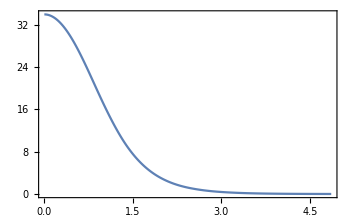

```mathematica
ListLinePlot[{Transpose[{Rdata,hdata}]}]
```

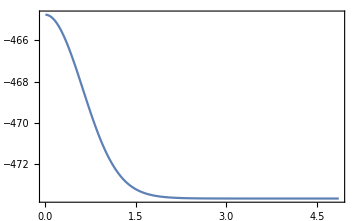

```mathematica
ListLinePlot[Transpose[{Rdata,Sdata}]]
```

```mathematica
hprofile[r_]:=Interpolation[Transpose[{Rdata,hdata}]][r]
Sprofile[r_]:=Interpolation[Transpose[{Rdata,Sdata}]][r]
```

```mathematica
Min[hdata]
```

0.014221

```mathematica
Kinh[r_]=1/2 hprofile'[r]^2;
KinS[r_]=1/2 Sprofile'[r]^2;
potential[r_]:=Vpotential[hprofile[r],Sprofile[r]]-Vpotential[Min[hdata],Min[Sdata]]
```

```mathematica
4π NIntegrate[r^2(Kinh[r]+KinS[r]+potential[r]),{r,0,Max[Rdata]}](*2d action*)
4π NIntegrate[r^2(Kinh[r]+potential[r]),{r,0,Max[Rdata]}](*1d action*)
```

2740.54

2538.59

The error between this and python is very small. So the computation method is correct.

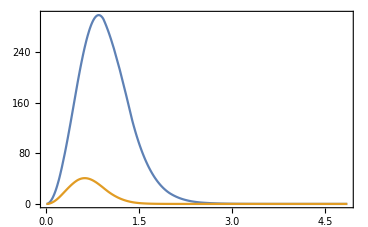

```mathematica
Plot[{Kinh[r],KinS[r]},{r,0,Max[Rdata]},PlotRange->Full]
```

```mathematica
A=15.08095388751636;
μS=31.037748419021955;
Ratio[r_]=(A/μS^2 hprofile[r])^2;(*Analytical solution of the ratio*)
```

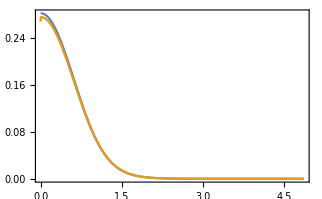

```mathematica
Plot[{Ratio[r],KinS[r]/Kinh[r]},{r,0,Max[Rdata]}]
```